## Load Data and Constant Values

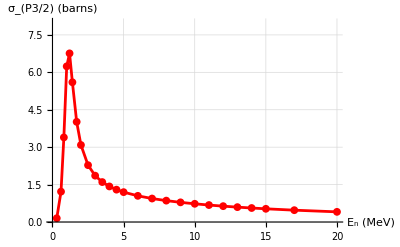

```mathematica
(* Load in CSV (Elab, δ (deg)) for P3/2 n+4He Elastic Scattering *)
data=Rest[Import[FileNameJoin[{NotebookDirectory[],"nalphaP32.csv"}],"Data"]];

(* Constants (Using Nuclear Units:MeV,fm,barns) *)
L = 1;
hbarc=197.32698;       (*MeV fm*)
mn=939.5654;           (*MeV*)
malpha=3727.3794;      (*MeV*)
mu=(mn*malpha)/(mn+malpha); (*MeV*)
h2m=(hbarc^2/(2*mu)); (*MeV fm^2*)
degToRad=Pi/180.;
fm2ToBarn=1/100.;

(* Kimenatic Stuff and Easier Bessels *)
Ecm[Elab_]:=Elab*(malpha/(mn+malpha));
K[Ecm_]:=Sqrt[2.0*mu*Ecm]/hbarc;
j1[k_,r_]:=SphericalBesselJ[L,k*r];
n1[k_,r_]:=SphericalBesselY[L,k*r];
h1[k_,r_]:=SphericalHankelH1[L,k*r];
h2[k_,r_]:=SphericalHankelH2[L,k*r];

(* Compute σ (barns) from loaded data *)
sigmaP32[Elab_,deltaDeg_]:=Module[{ecm,k,deltaRad},ecm=Ecm[Elab];
k=K[ecm];
deltaRad=deltaDeg*degToRad;
(8.0*Pi/k^2)*(Sin[deltaRad]^2)*fm2ToBarn];

(* Create list of (Elab,σ (barns) *)
sigmaP32Data = {#1,sigmaP32[#1,#2]}&@@@data;

ListLinePlot[sigmaP32Data,PlotMarkers->{Automatic,8},PlotStyle->Directive[Red],AxesLabel->{"\!\(\*SubscriptBox[\(E\), \(n\)]\) (MeV)","\!\(\*SubscriptBox[\(σ\), \(P3/2\)]\) (barns)"},PlotRange->{{0,20},{0,8}},GridLines->Automatic]
```

## Modeling with Effective Gaussian

```mathematica
(* Try two Gaussians, for the attractive well, one for the repulsive core*)
Veff[r_,c1_,a1_]:=c1*Exp[-(r/a1)^2]; 
radialODE=-h2m*u''[r]+(Veff[r,c1,a1]+h2m*L*(L+1)/r^2)*u[r]==Ecm*u[r];

(* Boundary conditions for L=1:u(r)~r^(L+1)->r^2, u is the reduced radial wavefunction *)
eps=10^-5;        (* Small non zero value to avoid 1/r^2 singularity *)
Rmax=15.0;        (* Radius (fm) for asymptotic matching *)
bc={u[eps]==eps^2,u'[eps]==2*eps};

(* ParametricNDSolveValue creates a compiled function which takes {Ecm,c1,a1,c2,a2} and outputs the wave function u and its derivative u' at Rmax *)solveWaveFunction=ParametricNDSolveValue[{radialODE,bc},{u[Rmax],u'[Rmax]},{r,eps,Rmax},{Ecm,c1,a1},Method->"StiffnessSwitching",MaxSteps->50000];

(* Define the exact asymptotic free solutions, call them J and Y, and their derivatives*)
J[k_,r_]:=r*j1[k,r]
Y[k_,r_]:=r*n1[k,r]
Jprime[k_,r_]:=Evaluate[D[r*j1[k,r],r]]
Yprime[k_,r_]:=Evaluate[D[r*n1[k,r],r]]

(* Extract Phase Shift in Degrees*)
PhaseShift[Ecm_?NumericQ,c1_?NumericQ,a1_?NumericQ]:=Module[{uR,uprimeR,gamma,currentK,Jval,Yval,Jpval,Ypval,num,den,delta},
{uR,uprimeR}=solveWaveFunction[Ecm,c1,a1];(*1. Get the numerical wavefunction and derivative at Rmax*)
gamma=uprimeR/uR;(*2. Compute the numerical logarithmic derivative*)
currentK=K[Ecm];
Jval=J[currentK,Rmax];(*3. Evaluate exact analytical Bessel functions at Rmax*)
Yval=Y[currentK,Rmax];
Jpval=Jprime[currentK,Rmax];
Ypval=Yprime[currentK,Rmax];
num=Jpval-gamma*Jval;(*4. Compute tan(delta) components*)
den=Ypval-gamma*Yval;
delta=ArcTan[den,num]*180/Pi;(*5. Get angle using ArcTan[x,y] to get the correct quadrant, convert to degrees*)
If[delta<0,delta=delta+180];(*Keep phase shift strictly positive/continuous for plotting*)
Return[delta];
]
```

## Optimize to fit Data

```mathematica
(*Define a Chi-Squared Error Function*)
ChiSquared[c1_?NumericQ,a1_?NumericQ]:=Sum[(PhaseShift[pt[[1]],c1,a1]-pt[[2]])^2,{pt,data}];

(*Initialize a tracker variable*)
currentStatus={"c1"->0,"a1"->0,"Chi2"->0};

(*Print a live-updating display*)
Print[Dynamic[Grid[List@@@currentStatus,Frame->All]]];

(*1. Define HARD physical constraints*)
constraints=c1<0&&1.0<=a1<=5.0; (*The depth must be attractive (negative),and the range strictly<5 fm (resonance is ~1-2fm)*)

(*Run the Optimizer*)
bestFit=NMinimize[{ChiSquared[c1,a1],constraints},{{c1,-80.0,-20.0},{a1,1.0,4.0}},Method->"NelderMead",
EvaluationMonitor:>(currentStatus={"c1"->c1,"a1"->a1,"Chi2"->ChiSquared[c1,a1]})]

(*Extract best parameters*)
{c1Fit,a1Fit}={c1,a1}/. bestFit[[2]];
```

{16.1877,{c1→-73.2983,a1→1.97385}}

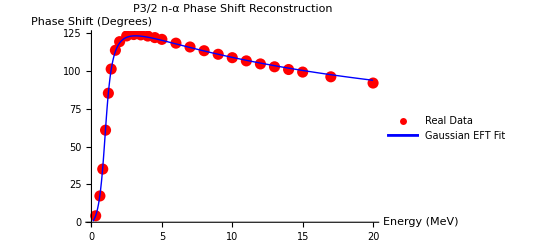

```mathematica
(*Plot the Victory!*)
Show[ListPlot[data,PlotStyle->{Red,PointSize[0.02]},PlotLegends->{"Real Data"}],Plot[PhaseShift[Ecm,c1Fit,a1Fit],{Ecm,0.1,20.0},PlotRange->All,PlotStyle->{Blue,Thick},PlotLegends->{"Gaussian EFT Fit"}],AxesLabel->{"Energy (MeV)","Phase Shift (Degrees)"},PlotLabel->"P3/2 n-α Phase Shift Reconstruction"]
```

## Analytic Continuation to Extract Pole

```mathematica
VeffFit[r_]:=Veff[r,c1Fit,a1Fit]; (* Redefined potential with fit parameters *)
Vlonshell[k_]:=1/(2*Pi^2)*NIntegrate[r^2*j1[k,r]^2*VeffFit[r],{r,eps,Rmax}]; (* V_l(k,k) in paper's conventions *)
Λ[k_]:=(I*2*Pi*mu*k)/(1-I*8*Pi^2*mu*k*Vlonshell[k]); (* Λ factor as defined in paper *)

(* IVP Superposition Solver for w(r)=G_V V|k>, this computes the solution to (H_0+V-E)w(r)=-V(r) r j_1(kr) *)SolveW[k_?NumericQ]:=Module[{Ecm,ODEreg,ODEp,ureg,up,gammaOut,Creg},Ecm=h2m*k^2;
ODEreg=-h2m*u''[r]+(VeffFit[r]+L*(L+1)*h2m/r^2-Ecm)*u[r]==0;(*1. Solve the Homogeneous Equation*)
ureg=NDSolveValue[{ODEreg,u[eps]==eps^(L+1),u'[eps]==(L+1)*eps^L},u,{r,eps,Rmax}];
ODEp=-h2m*p''[r]+(VeffFit[r]+L*(L+1)*h2m/r^2-Ecm)*p[r]==-VeffFit[r]*J[k,r]; (*2. Solve Inhomogeneous Equation*)
up=NDSolveValue[{ODEp,p[eps]==0,p'[eps]==0},p,{r,eps,Rmax}];
gammaOut=D[r*h1[k,r],r]/(r*h1[k,r])/. r->Rmax; (*3. Enforce Outgoing Robin Boundary Condition at Rmax *)
Creg=-(up'[Rmax]-gammaOut*up[Rmax])/(ureg'[Rmax]-gammaOut*ureg[Rmax]);(*4. Calculate coeff. of regular part*)
Function[r,up[r]+Creg*ureg[r]](*Return the wavefunction w(r)*)]

(* Evaluate the Matrix Element<k|V G_V V|k> *)
MatrixElement[k_?NumericQ]:=Module[{wFunc},wFunc=SolveW[k];
(1/(2*Pi^2))*NIntegrate[VeffFit[r]*J[k,r]*wFunc[r],{r,eps,Rmax}]]

(* Constraint Condition for Finding k_⋆ *)
PoleCondition[k_?NumericQ]:=1-Λ[k]*MatrixElement[k];
```

Searching the UHP for the resonance momentum...

Momentum Found: -0.246386-0.0636792 ⅈ

Physical Resonance Energy (MeV): 1.46978+0.81412 ⅈ

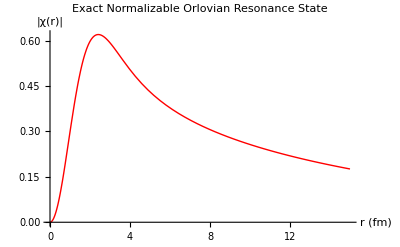

```mathematica
(* Find the Resonance Pole in the Lower Half Plane *)
Print["Searching the UHP for the resonance momentum..."];
(*Initial guess in UHP:k~-0.2+0.1 I *)kRoot=k/. FindRoot[PoleCondition[k]==0,{k,-0.24+0.06 I},Evaluated->False,AccuracyGoal->6,PrecisionGoal->6];

Print["Momentum Found: ",kRoot];
Print["Physical Resonance Energy (MeV): ",h2m*kRoot^2];

(*7. Extract the exact Orlovian Radial Resonance State*)
FinalOrlovianState[r_]:=Evaluate[Λ[-kRoot]*SolveW[-kRoot][r]];

(*Plot the magnitude of the Orlovian Bound State to verify exponential decay*)
Plot[Abs[FinalOrlovianState[r]],{r,eps,Rmax},PlotRange->All,PlotStyle->{Thick,Red},AxesLabel->{"r (fm)","|χ(r)|"},PlotLabel->"Exact Normalizable Orlovian Resonance State"]
```